# Flight challenge

En este anexo se muestra un ejemplo de  tratamiento del problema de planeadores para el Flight Challenge

```mathematica
Clear["Global`*"]
```

## Datos

```mathematica
bw=1.65;
cw=0.175;
bt=0.4;
ct=0.15;
h=0.75;
Λc4w=0;
Λc4t=0;
Λc2w=0;
Λc2t=0;
angCL0w=-5*Pi/180;
angCL0t=0;
CM0w=-0.09;
CM0t=0;
Sw=bw*cw
St=bt*ct
ARw=bw/cw
ARt=bt/ct
xCAw=0.25*cw
xCAt=cw+h+ct*0.25
Swet=1005441.079578089*10^-6;
```

0.28875

0.06

9.42857

2.66667

0.04375

0.9625

## CL

```mathematica
CLαw=2*Pi*(ARw/(2+Sqrt[4+ARw^2(1-Tan[Λc2w])]))
```

5.09019

```mathematica
CLαt=2*Pi*(ARt/(2+Sqrt[4+ARt^2(1-Tan[Λc2w])]))
```

3.14159

```mathematica
δϵδα=-16/Pi^3*CLαw/ARw
```

-0.278585

```mathematica
CL0w=CL0/.Flatten[Solve[0==CLαw*angCL0w+CL0,CL0]]
```

0.444203

```mathematica
CL0t=CL0/.Flatten[Solve[0==CLαw*angCL0t+CL0,CL0]]
```

0.

```mathematica
CLw=CL0w+CLαw*α
CLt=CL0t+CLαt*(1+δϵδα)*(α+δ)
```

0.444203+5.09019 α

0.+2.26639 (α+δ)

```mathematica
CL=CLw+CLt*St/Sw//Expand
```

0.444203+5.56113 α+0.470938 δ

## CM

```mathematica
CM=CM0w+CM0t*St*ct/Sw/cw+CLw*(xCAw-xCDG)/cw+CLt*(xCAt-xCDG)/cw
```

-0.09+5.71429 (0.04375-xCDG) (0.444203+5.09019 α)+5.71429 (0.9625-xCDG) (0.+2.26639 (α+δ))

```mathematica
xPN=xCDG/.Flatten[Solve[D[CM,α]==0,xCDG]]
```

0.326795

```mathematica
xCDG=0.08
```

0.08

Se toma este valor ya que está por delante del punto neutro.

```mathematica
δfα=δ/.Flatten[Solve[CM==0,δ]]//Expand
```

0.0159255-0.907744 α

### El trimado

Para trimar el avión suponemos que δ=0.ba.

```mathematica
δtrim=0;
```

```mathematica
αtrim=(α/.Flatten[Solve[δfα==δtrim,α]]);
αtrim*180/Pi
```

1.0052

El avión volará con 1.ba de ángulo de ataque.

¿Qué peso es capaz de levantar cuando vuela a 10m/s?

```mathematica
m10ms=1/2*1.225*10^2*Sw*CL/9.8/.α->αtrim/.δ->δtrim
```

0.977721

El avión volando a 10 m/s puede levantar casi 1 kg.

## Vuelo de planeo

```mathematica
Clear[v]
```

```mathematica
e=(1-0.045*ARw^0.68)*(1-0.227Λc4w^1.615)
ρ=1.225
m=1
g=9.81
CL=CL/.δ->δtrim/.α->αtrim
```

0.793064 (1-0.227 Λc4w^1.615)

1.225

1

9.81

0.541767

```mathematica
CD0=0.0055*Swet/Sw
CDi=CL^2/ARw/Pi/e
```

0.0191513

0.0123863

```mathematica
CD=CD0+CDi
```

0.0315375

```mathematica
Drag=1/2*ρ*v[t]^2*Sw*CD(*/.α->α[t]*)
Lift=1/2*ρ*v[t]^2*Sw*CL(*/.α->α[t]*)
W=g*m
```

0.0055777 v[t]^2

0.0958166 v[t]^2

9.81

```mathematica
z0=v*Sin[Pi/6]*t-1/2*g*t^2/.t->(t/.Flatten[Solve[0==v*Sin[Pi/6]-g*t]])
```

-4.905 (0.+0.0509684 v)^2+1/2 (0.+0.0509684 v) v

```mathematica
X=Integrate[W/Drag,{z,0,z0}]
```

(1758.79 (-4.905 (0.+0.0509684 v)^2+1/2 (0.+0.0509684 v) v))/v[t]^2

```mathematica
e1=m*D[v[t],t]==-Drag-W*Sin[γ[t]]
e2=m*v[t]*D[γ[t],t]==Lift-W*Cos[γ[t]]
e3=D[x[t],t]==v[t]*Cos[γ[t]]
e4=D[z[t],t]==v[t]*Sin[γ[t]]
```

v'[t]==-9.81 Sin[γ[t]]-0.0055777 v[t]^2

v[t] γ'[t]==-9.81 Cos[γ[t]]+0.0958166 v[t]^2

x'[t]==Cos[γ[t]] v[t]

z'[t]==Sin[γ[t]] v[t]

```mathematica
s=NDSolve[{e1,e2,e3,e4,v[0]==12,γ[0]==Pi/6,x[0]==0,z[0]==2*Sin[Pi/6]},{v,γ,x,z},{t,0,10}]
```

{{v→InterpolatingFunction[{{0.,10.}},<>],γ→InterpolatingFunction[{{0.,10.}},<>],x→InterpolatingFunction[{{0.,10.}},<>],z→InterpolatingFunction[{{0.,10.}},<>]}}

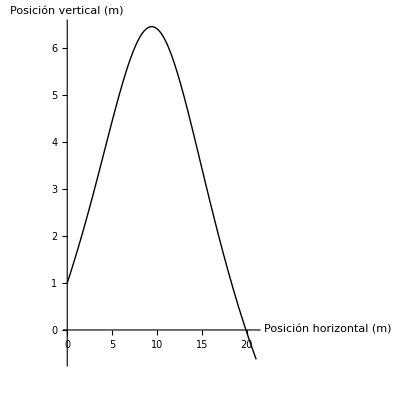

```mathematica
graf=ParametricPlot[Evaluate[{x[t],z[t]}/.s],{t,0,3},AspectRatio->1,AxesLabel->{"Posición horizontal (m)","Posición vertical (m)"},PlotStyle->Black]
```

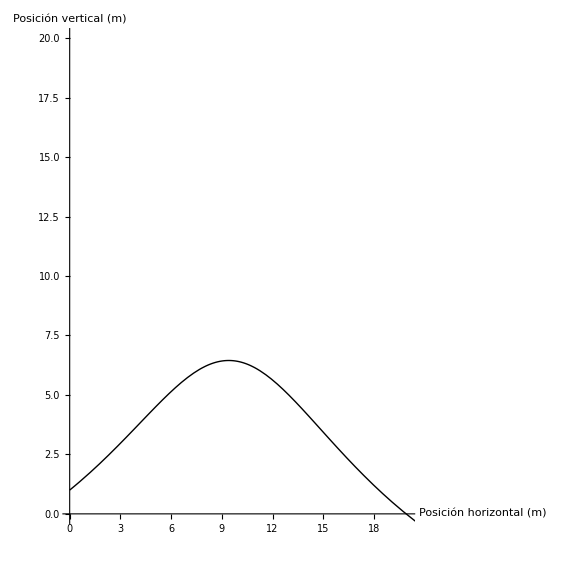

```mathematica
Show[graf,PlotRange->{{0,20},{0,20}}]
```